```mathematica
c2=0.54;
c1=1.4;
Dc=0.76;
Fc=0.5;
fc=0.093;
L1=1;
```

```mathematica
ap1=(-I)*(0.76+0.5)^2/(4*(0.093)^2*(2Pi)^4);
mpd=I*(-2*0.76)^2/(6*2*(0.093)^2*(2Pi)^4);
mpu=I*(-2*0.76)^2/(2*2*(0.093)^2*(2Pi)^4);
dp1=(-I)*(0.76+0.5)^2/(4*(0.093)^2*(2Pi)^4);
ep1=(-I)*(0.76+0.5)^2/(4*(0.093)^2*(2Pi)^4);
fp1=(I)*(0.76+0.5)^2/(4*(0.093)^2*(2Pi)^4);
gp1=(I)*(0.76+0.5)^2/(4*(0.093)^2*(2Pi)^4);
rsp1d=(-I)*(-2*0.76)^2/(6*2*(0.093)^2*(2Pi)^4);
rsp1u=(-I)*(-2*0.76)^2/(2*2*(0.093)^2*(2Pi)^4);
tup1d=(-I)*(-2*0.76)^2/(6*2*(0.093)^2*(2Pi)^4);
tup1u=(-I)*(-2*0.76)^2/(2*2*(0.093)^2*(2Pi)^4);
```

```mathematica
ap0=(-I)*(0.76+0.5)^2/(2*8*(0.093)^2*(2Pi)^4);
dp0=(-I)*(0.76+0.5)^2/(2*8*(0.093)^2*(2Pi)^4);
ep0=(-I)*(0.76+0.5)^2/(2*8*(0.093)^2*(2Pi)^4);
fp0=(I)*(0.76+0.5)^2/(2*8*(0.093)^2*(2Pi)^4);
gp0=(I)*(0.76+0.5)^2/(2*8*(0.093)^2*(2Pi)^4);
mp0=I*(-2*0.76)^2/(3*2*2*(0.093)^2*(2Pi)^4);
rsp0=(-I)*(-2*0.76)^2/(3*2*2*(0.093)^2*(2Pi)^4);
tup0=(-I)*(-2*0.76)^2/(3*2*2*(0.093)^2*(2Pi)^4);
```

```mathematica
a=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-a-xH-pi-zero.wdx"];
Ha=Query[1,1]@a;
Han=Interpolation[Flatten[Ha,1]];
Haf[x_,t_]=Han[x,t];

Ea=Query[2,1]@a;
Ean=Interpolation[Flatten[Ea,1]];
Eaf[x_,t_]=Ean[x,t];
```

```mathematica
d=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-d-xH-pi-zero.wdx"];
Hd=Query[1,1]@d;
Hdn=Interpolation[Flatten[Hd,1]];
Hdf[x_,t_]=Hdn[x,t];

Ed=Query[2,1]@d;
Edf[x_,t_]=Ed;
```

```mathematica
e=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-e-xH-pi-zero.wdx"];
He=Query[1,1]@e;
Hen=Interpolation[Flatten[He,1]];
Hef[x_,t_]=Hen[x,t];

Ee=Query[2,1]@e;
Eef[x_,t_]=Ee;
```

```mathematica
f=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-f-xH-pi-zero.wdx"];
Hf=Query[1,1]@f;
Hfn=Interpolation[Flatten[Hf,1]];
Hff[x_,t_]=Hfn[x,t];

Ef=Query[2,1]@f;
Efn=Interpolation[Flatten[Ef,1]];
Eff[x_,t_]=Efn[x,t];
```

```mathematica
g=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-g-xH-pi-zero.wdx"];
Hg=Query[1,1]@g;
Hgn=Interpolation[Flatten[Hg,1]];
Hgf[x_,t_]=Hgn[x,t];

Eg=Query[2,1]@g;
Egn=Interpolation[Flatten[Eg,1]];
Egf[x_,t_]=Egn[x,t];
```

```mathematica
m=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-m-xH-pi-zero.wdx"];
Hm=Query[1,1]@m;
Hmn=Interpolation[Flatten[Hm,1]];
Hmf[x_,t_]=Hmn[x,t];

Em=Query[2,1]@m;
Emn=Interpolation[Flatten[Em,1]];
Emf[x_,t_]=Emn[x,t];
```

```mathematica
rs=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-rs-xH-pi-zero.wdx"];
Hrs=Query[1,1]@rs;
Hrsn=Interpolation[Flatten[Hrs,1]];
Hrsf[x_,t_]=Hrsn[x,t];

Ers=Query[2,1]@rs;
Ersn=Interpolation[Flatten[Ers,1]];
Ersf[x_,t_]=Ersn[x,t];
```

```mathematica
tu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-tu-xH-pi-zero.wdx"];
Htu=Query[1,1]@tu;
Htun=Interpolation[Flatten[Htu,1]];
Htuf[x_,t_]=Htun[x,t];

Etu=Query[2,1]@tu;
Etun=Interpolation[Flatten[Etu,1]];
Etuf[x_,t_]=Etun[x,t];
```

```mathematica
Had[x_,t_]=ap1*Haf[x,t];
Ead[x_,t_]=ap1*Eaf[x,t];
Hdd[x_,t_]=dp1*Hdf[x,t];
Edd[x_,t_]=dp1*Edf[x,t];
Hed[x_,t_]=ep1*Hef[x,t];
Eed[x_,t_]=ep1*Eef[x,t];
Hfd[x_,t_]=fp1*Hff[x,t];
Efd[x_,t_]=fp1*Eff[x,t];
Hgd[x_,t_]=gp1*Hgf[x,t];
Egd[x_,t_]=gp1*Egf[x,t];

Hap0d[x_,t_]=ap0*Haf[x,t];
Eap0d[x_,t_]=ap0*Eaf[x,t];
Hdp0d[x_,t_]=dp0*Hdf[x,t];
Edp0d[x_,t_]=dp0*Edf[x,t];
Hep0d[x_,t_]=ep0*Hef[x,t];
Eep0d[x_,t_]=ep0*Eef[x,t];
Hfp0d[x_,t_]=fp0*Hff[x,t];
Efp0d[x_,t_]=fp0*Eff[x,t];
Hgp0d[x_,t_]=gp0*Hgf[x,t];
Egp0d[x_,t_]=gp0*Egf[x,t];

Hap0u[x_,t_]=ap0*Haf[x,t];
Eap0u[x_,t_]=ap0*Eaf[x,t];
Hdp0u[x_,t_]=dp0*Hdf[x,t];
Edp0u[x_,t_]=dp0*Edf[x,t];
Hep0u[x_,t_]=ep0*Hef[x,t];
Eep0u[x_,t_]=ep0*Eef[x,t];
Hfp0u[x_,t_]=fp0*Hff[x,t];
Efp0u[x_,t_]=fp0*Eff[x,t];
Hgp0u[x_,t_]=gp0*Hgf[x,t];
Egp0u[x_,t_]=gp0*Egf[x,t];

Hmd[x_,t_]=mpd*Hmf[x,t];
Emd[x_,t_]=mpd*Emf[x,t];
Hmu[x_,t_]=mpu*Hmf[x,t];
Emu[x_,t_]=mpu*Emf[x,t];

Hmp0d[x_,t_]=mp0*Hmf[x,t];
Emp0d[x_,t_]=mp0*Emf[x,t];
Hmp0u[x_,t_]=mp0*Hmf[x,t];
Emp0u[x_,t_]=mp0*Emf[x,t];

Hrsd[x_,t_]=rsp1d*Hrsf[x,t];
Ersd[x_,t_]=rsp1d*Ersf[x,t];
Hrsu[x_,t_]=rsp1u*Hrsf[x,t];
Ersu[x_,t_]=rsp1u*Ersf[x,t];

Hrsp0d[x_,t_]=rsp0*Hrsf[x,t];
Ersp0d[x_,t_]=rsp0*Ersf[x,t];
Hrsp0u[x_,t_]=rsp0*Hrsf[x,t];
Ersp0u[x_,t_]=rsp0*Ersf[x,t];


Htud[x_,t_]=tup1d*Htuf[x,t];
Etud[x_,t_]=tup1d*Etuf[x,t];
Htuu[x_,t_]=tup1u*Htuf[x,t];
Etuu[x_,t_]=tup1u*Etuf[x,t];

Htup0d[x_,t_]=tup0*Htuf[x,t];
Etup0d[x_,t_]=tup0*Etuf[x,t];
Htup0u[x_,t_]=tup0*Htuf[x,t];
Etup0u[x_,t_]=tup0*Etuf[x,t];
```

```mathematica
(*x*(dbar-ubar)*)
```

```mathematica
Hdubar[x_,t_]=Had[x,t]+Hdd[x,t]+Hed[x,t]+Hfd[x,t]+Hgd[x,t]+Hmd[x,t]+Hrsd[x,t]+Htud[x,t]-(Hmu[x,t]+Hrsu[x,t]+Htuu[x,t]);
Edubar[x_,t_]=Ead[x,t]+Edd[x,t]+Eed[x,t]+Efd[x,t]+Egd[x,t]+Emd[x,t]+Ersd[x,t]+Etud[x,t]-(Emu[x,t]+Ersu[x,t]+Etuu[x,t]);
```

```mathematica
(*dbar/ubar*)
```

```mathematica
Hdude[x_,t_]=(Had[x,t]+Hdd[x,t]+Hed[x,t]+Hfd[x,t]+Hgd[x,t]+Hmd[x,t]+Hrsd[x,t]+Htud[x,t]+Hap0d[x,t]+Hdp0d[x,t]+Hep0d[x,t]+Hfp0d[x,t]+Hgp0d[x,t]+Hmp0d[x,t]+Hrsp0d[x,t]+Htup0d[x,t])/(Hmu[x,t]+Hrsu[x,t]+Htuu[x,t]+Hap0u[x,t]+Hdp0u[x,t]+Hep0u[x,t]+Hfp0u[x,t]+Hgp0u[x,t]+Hmp0u[x,t]+Hrsp0u[x,t]+Htup0u[x,t]);
Edude[x_,t_]=(Ead[x,t]+Edd[x,t]+Eed[x,t]+Efd[x,t]+Egd[x,t]+Emd[x,t]+Ersd[x,t]+Etud[x,t]+Eap0d[x,t]+Edp0d[x,t]+Eep0d[x,t]+Efp0d[x,t]+Egp0d[x,t]+Emp0d[x,t]+Ersp0d[x,t]+Etup0d[x,t])/(Emu[x,t]+Ersu[x,t]+Etuu[x,t]+Eap0u[x,t]+Edp0u[x,t]+Eep0u[x,t]+Efp0u[x,t]+Egp0u[x,t]+Emp0u[x,t]+Ersp0u[x,t]+Etup0u[x,t]);
```

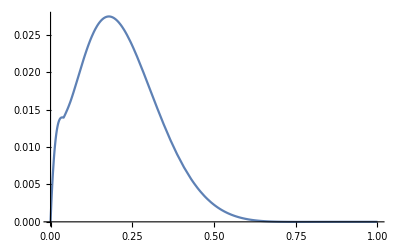

```mathematica
Plot[Hdubar[x,0],{x,0,1}]
```

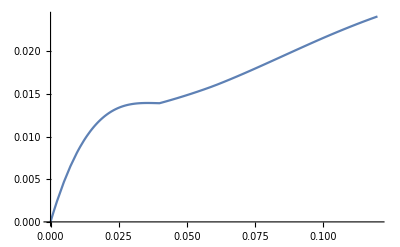

```mathematica
Plot[Hdubar[x,0],{x,0,0.12}]
```

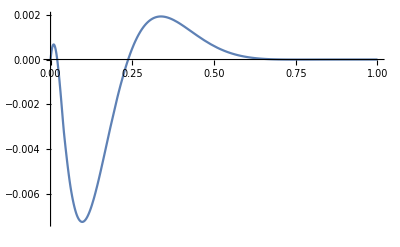

```mathematica
Plot[Hdubar[x,-1],{x,0,1}]
```

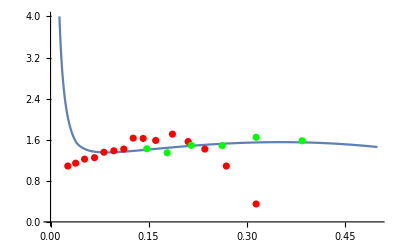

```mathematica
Show[Plot[Hdude[x,0],{x,0.01,0.5},PlotRange->{Automatic,{0,4}}],ListPlot[dcuE866data,PlotStyle->Red],ListPlot[dcuE906data,PlotStyle->Green]]
```

```mathematica
Hdude[0.31,0]
```

1.54559+0. ⅈ

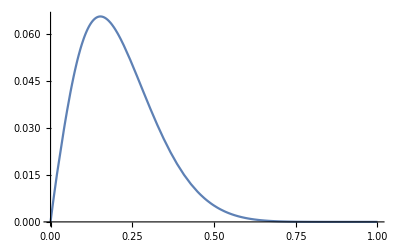

```mathematica
Plot[Had[x,0]+Hdd[x,0]+Hed[x,0]+Hfd[x,0]+Hgd[x,0]+Hmd[x,0]+Hrsd[x,0]+Htud[x,0],{x,0,1}]
```

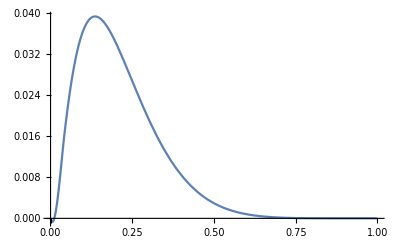

```mathematica
Plot[Hmu[x,0]+Hrsu[x,0]+Htuu[x,0],{x,0,1}]
```

```mathematica
Hmeson[x_,t_]=Had[x,t]+Hmd[x,t]-(Hmu[x,t]);
Emeson[x_,t_]=Ead[x,t]+Emd[x,t]-(Emu[x,t]);
```

```mathematica
Hmede[x_,t_]=(Had[x,t]+Hmd[x,t]+Hap0d[x,t]+Hmp0d[x,t])/(Hmu[x,t]+Hap0u[x,t]+Hmp0u[x,t]);
Emede[x_,t_]=(Ead[x,t]+Emd[x,t]+Eap0d[x,t]+Emp0d[x,t])/(Emu[x,t]+Eap0u[x,t]+Emp0u[x,t]);
```

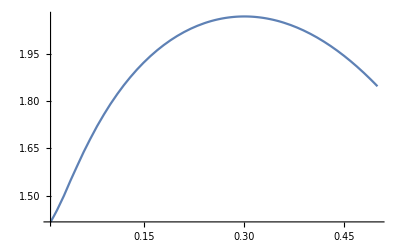

```mathematica
Plot[Hmede[x,0],{x,0.01,0.5}]
```

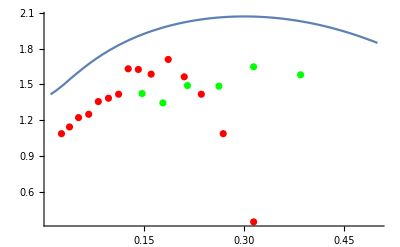

```mathematica
Show[Plot[Hmede[x,0],{x,0.01,0.5},PlotRange->All],ListPlot[dcuE866data,PlotStyle->Red],ListPlot[dcuE906data,PlotStyle->Green]]
```

```mathematica
Hmede[0.31,0]
```

2.06834+0. ⅈ

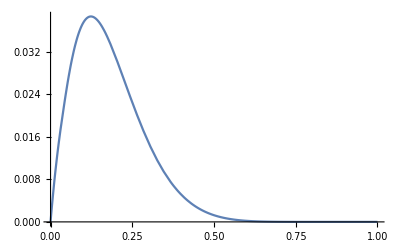

```mathematica
Plot[Hmeson[x,0],{x,0,1}]
```

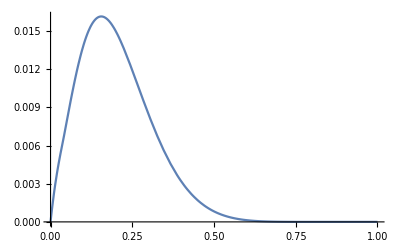

```mathematica
Plot[Hmeson[x,-0.25],{x,0,1}]
```

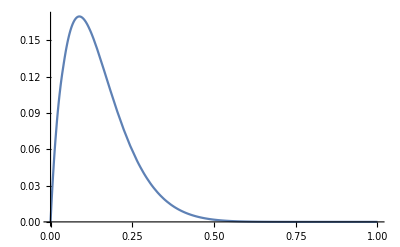

```mathematica
Plot[Emeson[x,0],{x,0,1}]
```

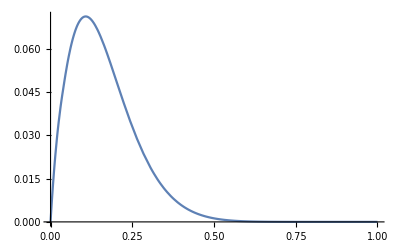

```mathematica
Plot[Emeson[x,-0.25],{x,0,1}]
```

```mathematica
Hkr[x_,t_]=Hdd[x,t]+Hed[x,t]+Hfd[x,t]+Hgd[x,t]+Hrsd[x,t]+Htud[x,t]-(Hrsu[x,t]+Htuu[x,t]);
Ekr[x_,t_]=Edd[x,t]+Eed[x,t]+Efd[x,t]+Egd[x,t]+Ersd[x,t]+Etud[x,t]-(Ersu[x,t]+Etuu[x,t]);
```

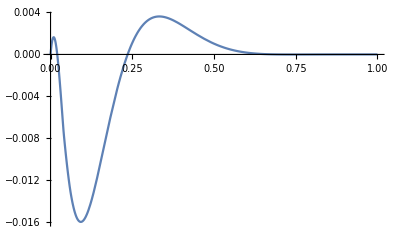

```mathematica
Plot[Hkr[x,0],{x,0,1}]
```

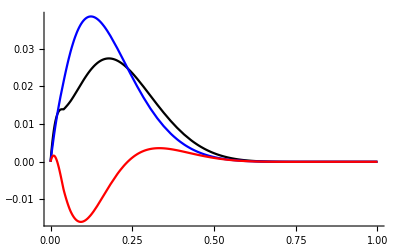

```mathematica
Show[Plot[Hdubar[x,0],{x,0,1},PlotStyle->Black,PlotRange->All],Plot[Hmeson[x,0],{x,0,1},PlotStyle->Blue,PlotRange->All],Plot[Hkr[x,0],{x,0,1},PlotStyle->Red,PlotRange->All]]
```

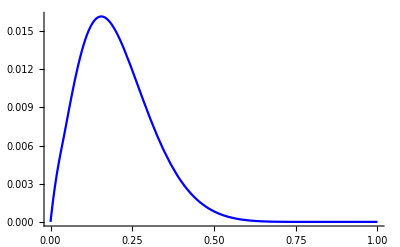

```mathematica
Plot[Hmeson[x,-0.25],{x,0,1},PlotStyle->Blue,PlotRange->All]
```

```mathematica
Hmeson[0.2,-0.25]
```

0.0149718+0. ⅈ

```mathematica
Hmeson[0.16,-0.25]
```

0.0161363+0. ⅈ

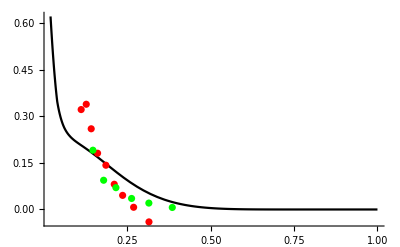

```mathematica
Show[Plot[(1/x)*Hdubar[x,0],{x,0.02,1},PlotStyle->Black,PlotRange->All],ListPlot[dmuE866,PlotStyle->Red],ListPlot[dmuE906,PlotStyle->Green]]
```

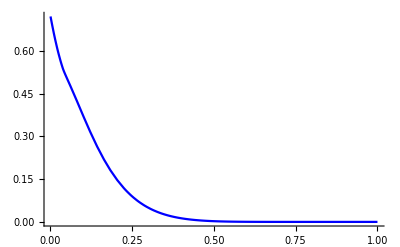

```mathematica
Plot[(1/x)*Hmeson[x,0],{x,0.001,1},PlotStyle->Blue,PlotRange->All]
```

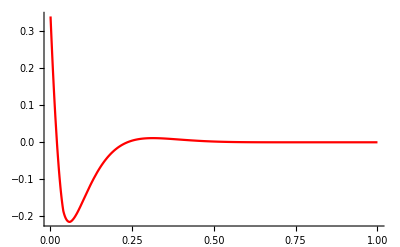

```mathematica
Plot[(1/x)*Hkr[x,0],{x,0.001,1},PlotStyle->Red,PlotRange->All]
```

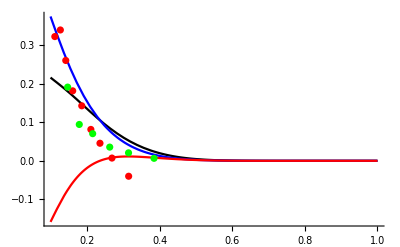

```mathematica
Show[Plot[(1/x)*Hdubar[x,0],{x,0.1,1},PlotStyle->Black,PlotRange->All],Plot[(1/x)*Hmeson[x,0],{x,0.1,1},PlotStyle->Blue,PlotRange->All],Plot[(1/x)*Hkr[x,0],{x,0.1,1},PlotStyle->Red,PlotRange->All],ListPlot[dmuE866,PlotStyle->Red],ListPlot[dmuE906,PlotStyle->Green]]
```

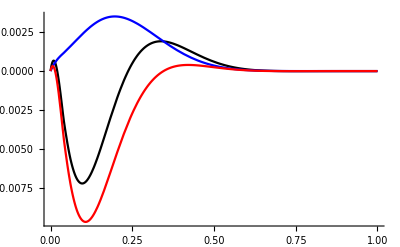

```mathematica
Show[Plot[Hdubar[x,-1],{x,0,1},PlotStyle->Black,PlotRange->All],Plot[Hmeson[x,-1],{x,0,1},PlotStyle->Blue,PlotRange->All],Plot[Hkr[x,-1],{x,0,1},PlotStyle->Red,PlotRange->All]]
```

```mathematica
dcuE866data={{0.026400000000000035,1.087686567164179},
{0.038400000000000045,1.1436567164179103},
{0.052000000000000046,1.2220149253731343},
{0.06720000000000001,1.25},
{0.08160000000000003,1.3563432835820894},
{0.09680000000000002,1.3843283582089554},
{0.11200000000000002,1.4179104477611941},
{0.1264,1.630597014925373},
{0.1416,1.625},
{0.1608,1.585820895522388},
{0.1864,1.7089552238805972},
{0.21040000000000003,1.5634328358208955},
{0.236,1.4179104477611941},
{0.2688,1.087686567164179},
{0.3144,0.34888059701492535}
};
```

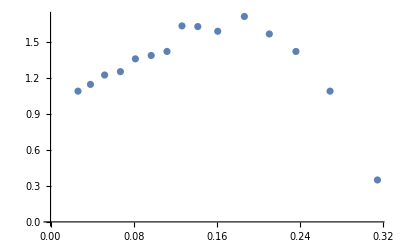

```mathematica
ListPlot[dcuE866data]
```

```mathematica
dcuE906data={{0.1472,1.4235074626865671},
{0.1784,1.3451492537313434},
{0.21519999999999995,1.4906716417910448},
{0.2624,1.4850746268656716},
{0.3144,1.6473880597014925},
{0.3848,1.580223880597015}
};
```

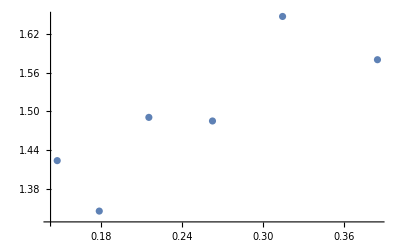

```mathematica
ListPlot[dcuE906data]
```

```mathematica
dmuE906={{0.1470873786407767,0.19096774193548385},
{0.17912621359223302,0.09419354838709676},
{0.21601941747572817,0.07032258064516128},
{0.26294498381877024,0.03548387096774186},
{0.31472491909385114,0.02064516129032251},
{0.3849514563106797,0.006451612903225767}
};
```

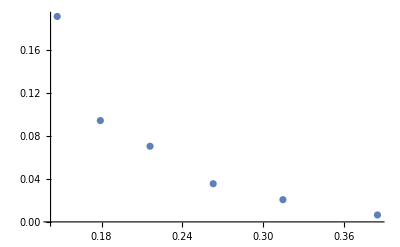

```mathematica
ListPlot[dmuE906]
```

```mathematica
dmuE866={{0.11181229773462781,0.3219354838709677},
{0.1270226537216828,0.3390322580645161},
{0.1419093851132686,0.26},
{0.16100323624595467,0.18129032258064515},
{0.18592233009708736,0.14258064516129032},
{0.21100323624595468,0.08129032258064517},
{0.23608414239482206,0.04548387096774198},
{0.2690938511326861,0.007096774193548427},
{0.3150485436893204,-0.03999999999999998}
};
```

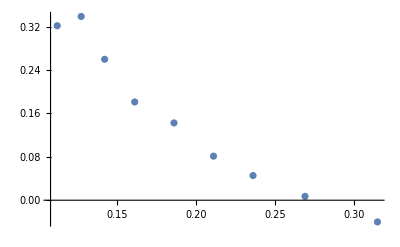

```mathematica
ListPlot[dmuE866]
```

```mathematica
(*好像把纵坐标取大了10倍*)
```

```mathematica
Hexdubardata={{0.0016853932584269815,0.01092436974789912},
{0.003932584269662948,0.03445378151260503},
{0.008426966292134852,0.06890756302521006},
{0.012359550561797772,0.08907563025210086},
{0.015168539325842723,0.11260504201680666},
{0.017977528089887646,0.126890756302521},
{0.020786516853932596,0.14285714285714285},
{0.023033707865168562,0.16386554621848737},
{0.027528089887640467,0.180672268907563},
{0.03033707865168539,0.20420168067226885},
{0.03426966292134834,0.22436974789915964},
{0.03876404494382024,0.24621848739495794},
{0.043258426966292146,0.2680672268907563},
{0.047191011235955066,0.28823529411764703},
{0.04943820224719103,0.303781512605042},
{0.05674157303370789,0.3285714285714285},
{0.061797752808988776,0.346218487394958},
{0.07303370786516855,0.3705882352941176},
{0.07921348314606744,0.38655462184873945},
{0.09213483146067417,0.4033613445378151},
{0.10449438202247194,0.41512605042016804},
{0.11910112359550559,0.41764705882352937},
{0.13202247191011238,0.41470588235294115},
{0.14438202247191015,0.4058823529411764},
{0.15168539325842692,0.3974789915966386},
{0.15786516853932583,0.39033613445378146},
{0.1662921348314607,0.3810924369747899},
{0.1780898876404494,0.3638655462184874},
{0.18820224719101122,0.35168067226890753},
{0.19550561797752805,0.34033613445378147},
{0.19999999999999998,0.32689075630252096},
{0.20786516853932582,0.31596638655462184},
{0.21573033707865166,0.30336134453781505},
{0.22528089887640448,0.2848739495798319},
{0.23707865168539324,0.2663865546218487},
{0.2528089887640449,0.2394957983193277},
{0.2696629213483146,0.21428571428571425},
{0.2808988764044943,0.19999999999999996},
{0.29157303370786514,0.17815126050420166},
{0.3050561797752809,0.1605042016806722},
{0.3134831460674158,0.1504201680672268},
{0.32191011235955047,0.13613445378151257},
{0.3387640449438202,0.11512605042016799},
{0.35,0.10420168067226887},
{0.36460674157303363,0.08991596638655464},
{0.3792134831460674,0.07563025210084029},
{0.396067415730337,0.06386554621848739},
{0.41067415730337065,0.055462184873949494},
{0.4241573033707865,0.042857142857142816},
{0.44269662921348296,0.03529411764705881},
{0.46292134831460663,0.026050420168067245},
{0.48370786516853925,0.02184873949579824},
{0.5016853932584269,0.015966386554621792},
{0.5191011235955055,0.014285714285714235},
{0.5376404494382021,0.010084033613445342},
{0.5623595505617976,0.004201680672268893},
{0.5853932584269661,0.004201680672268893},
{0.5983146067415729,0.0008403361344537785}
};
```

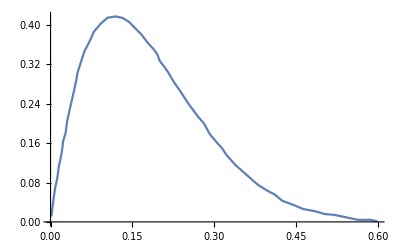

InterpolatingFunction::dmval: Input value {0.0000122571} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
ListLinePlot[Hexdubardata]
```

```mathematica
FindFit[Hexdubardata,]
```

```mathematica
Fit[Hexdubardata, {1,x,x^2,x^3,x^4,x^5}, x]
```

-0.00860937+8.84934 x-61.2005 x^2+163.174 x^3-197.352 x^4+90.8487 x^5

```mathematica
Hexdubar[x_]=-0.008609374368660145+8.849341692528956 x-61.20048373887701 x^2+163.17446188487307 x^3-197.35237919589093 x^4+90.84866778717655 x^5;
```

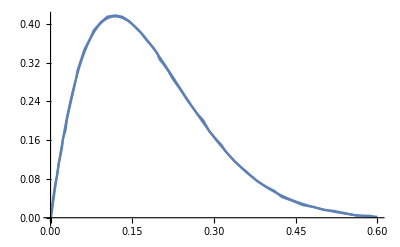

```mathematica
Show[Plot[Hexdubar[x],{x,0,0.6}],ListLinePlot[Hexdubardata]]
```

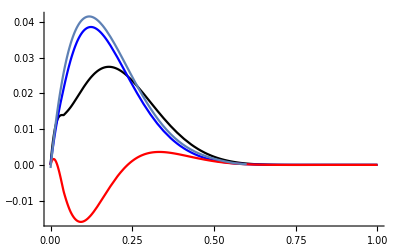

```mathematica
Show[Plot[Hdubar[x,0],{x,0,1},PlotStyle->Black,PlotRange->All],Plot[Hmeson[x,0],{x,0,1},PlotStyle->Blue,PlotRange->All],Plot[Hkr[x,0],{x,0,1},PlotStyle->Red,PlotRange->All],Plot[(1/10)*Hexdubar[x],{x,0,0.6}]]
```

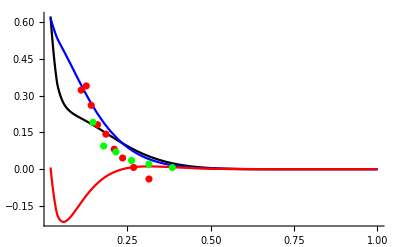

```mathematica
picdubar=Show[Plot[(1/x)*Hdubar[x,0],{x,0.02,1},PlotStyle->Black,PlotRange->All],Plot[(1/x)*Hmeson[x,0],{x,0.02,1},PlotStyle->Blue,PlotRange->All],Plot[(1/x)*Hkr[x,0],{x,0.02,1},PlotStyle->Red,PlotRange->All],ListPlot[dmuE866,PlotStyle->Red],ListPlot[dmuE906,PlotStyle->Green]]
```

```mathematica
pathdubar=FileNameJoin[{"G:\\calc-online\\gpd\\formfactor\\lowestorder\\result",
"dubar.pdf"}];
Export[pathdubar,picdubar]
```

G:\calc-online\gpd\formfactor\lowestorder\result\dubar.pdf

InterpolatingFunction::dmval: Input value {0.0000204286,0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

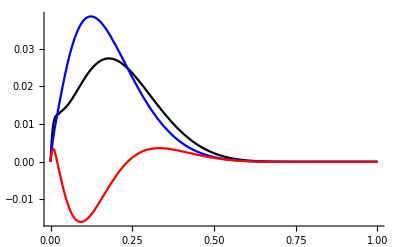

```mathematica
picxdubar=Show[Plot[x*Hdubar[x,0],{x,0,1},PlotStyle->Black,PlotRange->All],Plot[x*Hmeson[x,0],{x,0,1},PlotStyle->Blue,PlotRange->All],Plot[x*Hkr[x,0],{x,0,1},PlotStyle->Red,PlotRange->All]]
```

```mathematica
pathxdubar=FileNameJoin[{"G:\\calc-online\\gpd\\formfactor\\lowestorder\\result",
"xdubar.pdf"}];
Export[pathxdubar,picxdubar]
```

G:\calc-online\gpd\formfactor\lowestorder\result\xdubar.pdf

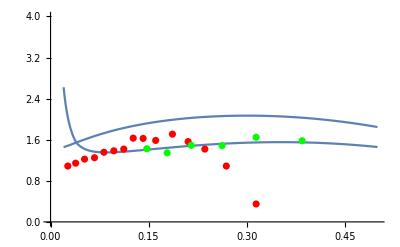

```mathematica
picdcu=Show[Plot[Hdude[x,0],{x,0.02,0.5},PlotRange->{Automatic,{0,4}}],Plot[Hmede[x,0],{x,0.02,0.5},PlotRange->All],ListPlot[dcuE866data,PlotStyle->Red],ListPlot[dcuE906data,PlotStyle->Green]]
```